```mathematica
(* data:{Subscript[x, i],Subscript[y, i]};
fitting function:f(x);
χ^2=∑_i (|Subscript[r, i]|)^2,Subscript[r, i]=f(Subscript[x, i])-Subscript[y, i];
Least squares:minimize χ^2 with respect to parameters(对于参数) *)
```

```mathematica
y[x_]:=2*x+3;
mydata=Table[{x,y[x]},{x,-1,5}]
```

{{-1,1},{0,3},{1,5},{2,7},{3,9},{4,11},{5,13}}

```mathematica
Fit[mydata,{1,x},x]
```

3.+2. x

```mathematica
mydata2=Table[{x,y[x]+RandomReal[{-1,1}]},{x,-1,5}]
```

{{-1,0.925146},{0,3.6261},{1,4.71516},{2,7.84753},{3,9.51943},{4,11.5691},{5,13.5587}}

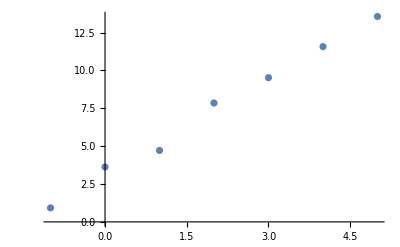

```mathematica
ListPlot[mydata2]
```

```mathematica
Fit[mydata2,{1,x},x]
```

3.20938+2.09254 x

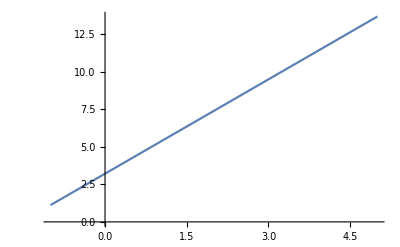

```mathematica
Plot[3.2093829989903164+2.0925367241946082 x,{x,-1,5}]
```

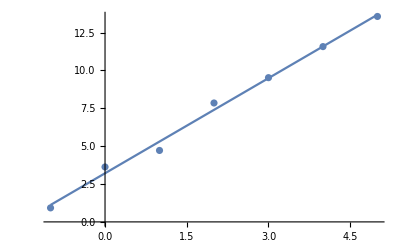

```mathematica
dataplot=ListPlot[mydata2];
fitplot=Plot[3.2093829989903164+2.0925367241946082 x,{x,-1,5}];
Show[dataplot,fitplot]
```